```mathematica
pts=Import["~/w2013/stat245/scripts_5/data","List"]
```

{14.27,15.15,13.98,15.4,14.04,14.1,13.75,14.23,14.8,13.98,14.47,14.68,13.68,15.47,14.87,14.44,12.28,14.9,14.65,13.33,15.31,13.73,15.28,14.57,17.09,15.91,14.73,14.41,14.32,13.65,14.43,15.1,14.52,15.18,14.19,13.64,15.02,13.96,12.92,15.63,14.49,15.21,14.77,14.01,14.57,15.56,13.83,14.56,14.75,14.3,14.92,15.49,15.38,13.66,15.03,14.41,14.62,15.47,15.13}

```mathematica
Sort[pts]
```

{12.28,12.92,13.33,13.64,13.65,13.66,13.68,13.73,13.75,13.83,13.96,13.98,13.98,14.01,14.04,14.1,14.19,14.23,14.27,14.3,14.32,14.41,14.41,14.43,14.44,14.47,14.49,14.52,14.56,14.57,14.57,14.62,14.65,14.68,14.73,14.75,14.77,14.8,14.87,14.9,14.92,15.02,15.03,15.1,15.13,15.15,15.18,15.21,15.28,15.31,15.38,15.4,15.47,15.47,15.49,15.56,15.63,15.91,17.09}

```mathematica
pts
```

{14.27,15.15,13.98,15.4,14.04,14.1,13.75,14.23,14.8,13.98,14.47,14.68,13.68,15.47,14.87,14.44,12.28,14.9,14.65,13.33,15.31,13.73,15.28,14.57,17.09,15.91,14.73,14.41,14.32,13.65,14.43,15.1,14.52,15.18,14.19,13.64,15.02,13.96,12.92,15.63,14.49,15.21,14.77,14.01,14.57,15.56,13.83,14.56,14.75,14.3,14.92,15.49,15.38,13.66,15.03,14.41,14.62,15.47,15.13}

```mathematica
pts=Sort[pts]
```

{12.28,12.92,13.33,13.64,13.65,13.66,13.68,13.73,13.75,13.83,13.96,13.98,13.98,14.01,14.04,14.1,14.19,14.23,14.27,14.3,14.32,14.41,14.41,14.43,14.44,14.47,14.49,14.52,14.56,14.57,14.57,14.62,14.65,14.68,14.73,14.75,14.77,14.8,14.87,14.9,14.92,15.02,15.03,15.1,15.13,15.15,15.18,15.21,15.28,15.31,15.38,15.4,15.47,15.47,15.49,15.56,15.63,15.91,17.09}

```mathematica
m=Mean[pts]
```

14.58

```mathematica
s=StandardDeviation[pts]
```

0.77642

```mathematica
dist=NormalDistribution[m,s]
```

NormalDistribution[14.58,0.77642]

```mathematica
nlist=Range[Length[pts]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59}

```mathematica
nlist/=Length[pts]+1
```

{1/60,1/30,1/20,1/15,1/12,1/10,7/60,2/15,3/20,1/6,11/60,1/5,13/60,7/30,1/4,4/15,17/60,3/10,19/60,1/3,7/20,11/30,23/60,2/5,5/12,13/30,9/20,7/15,29/60,1/2,31/60,8/15,11/20,17/30,7/12,3/5,37/60,19/30,13/20,2/3,41/60,7/10,43/60,11/15,3/4,23/30,47/60,4/5,49/60,5/6,17/20,13/15,53/60,9/10,11/12,14/15,19/20,29/30,59/60}

```mathematica
nvec=Map[Function[InverseCDF[dist,#]],nlist]
```

{12.9277,13.1561,13.3029,13.4145,13.5062,13.585,13.6547,13.7176,13.7753,13.8289,13.8791,13.9265,13.9717,14.0148,14.0563,14.0963,14.1351,14.1728,14.2096,14.2456,14.2808,14.3155,14.3496,14.3833,14.4166,14.4496,14.4824,14.5151,14.5476,14.58,14.6124,14.6449,14.6776,14.7104,14.7434,14.7767,14.8104,14.8445,14.8792,14.9144,14.9504,14.9872,15.0249,15.0637,15.1037,15.1452,15.1883,15.2335,15.2809,15.3311,15.3847,15.4424,15.5053,15.575,15.6538,15.7455,15.8571,16.0039,16.2323}

```mathematica
plotted=Thread[Function[{#1,#2}][pts,nvec]]
```

{{12.28,12.9277},{12.92,13.1561},{13.33,13.3029},{13.64,13.4145},{13.65,13.5062},{13.66,13.585},{13.68,13.6547},{13.73,13.7176},{13.75,13.7753},{13.83,13.8289},{13.96,13.8791},{13.98,13.9265},{13.98,13.9717},{14.01,14.0148},{14.04,14.0563},{14.1,14.0963},{14.19,14.1351},{14.23,14.1728},{14.27,14.2096},{14.3,14.2456},{14.32,14.2808},{14.41,14.3155},{14.41,14.3496},{14.43,14.3833},{14.44,14.4166},{14.47,14.4496},{14.49,14.4824},{14.52,14.5151},{14.56,14.5476},{14.57,14.58},{14.57,14.6124},{14.62,14.6449},{14.65,14.6776},{14.68,14.7104},{14.73,14.7434},{14.75,14.7767},{14.77,14.8104},{14.8,14.8445},{14.87,14.8792},{14.9,14.9144},{14.92,14.9504},{15.02,14.9872},{15.03,15.0249},{15.1,15.0637},{15.13,15.1037},{15.15,15.1452},{15.18,15.1883},{15.21,15.2335},{15.28,15.2809},{15.31,15.3311},{15.38,15.3847},{15.4,15.4424},{15.47,15.5053},{15.47,15.575},{15.49,15.6538},{15.56,15.7455},{15.63,15.8571},{15.91,16.0039},{17.09,16.2323}}

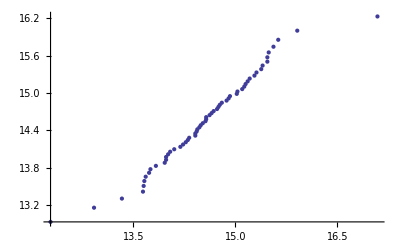

```mathematica
qq=ListPlot[plotted]
```

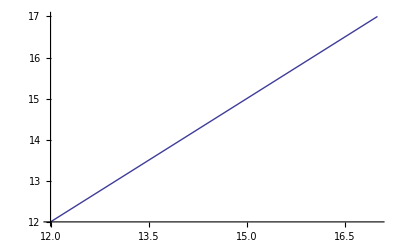

```mathematica
yx=Plot[x,{x,12,17}]
```

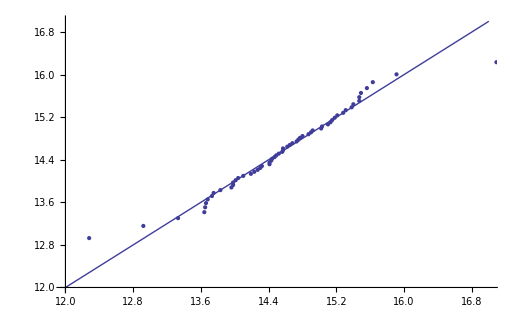

```mathematica
Show[yx,qq]
```